## Variable internal stores (1 nutrient)

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Aux[R]->{Equation:>a(Rin-R)-v[R]n},
Pop[pop]->{
Component[Q]:>{Equation:>v[R]-μ[Q]Q,Type->"Intensive"},
Component[n]:>{Equation:>(μ[Q]-m)n}
},
Parameters:>{a>0,Rin>0,vmax>0,H>0,μ∞>0,Qmin>0,m>0(*,v,μ*)}
}]
```

```mathematica
v[R_]:=vmax R/(R+H);
μ[Q_]:=μ∞(1-Qmin/Q);
```

```mathematica
a=1;
Rin=10;
vmax=10;
H=1;
μ∞=2;
Qmin=1;
m=0.5;
```

```mathematica
sol=EcoSim[{R->Rin,Q->Qmin,n->0.01},20];
```

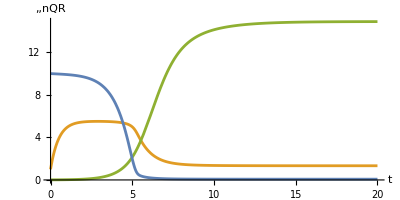

{Q→1.33348,n→14.8879,R→0.0714542}

```mathematica
PlotDynamics[sol,AspectRatio->1/2]
FinalSlice[sol]
```

Some analytical calculations:

```mathematica
ClearParameters
```

```mathematica
(* QSS Q *)
qss=SolveEcoEq[{Q},QSS->True]
```

{{Q→(R vmax+H Qmin μ∞+Qmin R μ∞)/((H+R) μ∞)}}

```mathematica
(* growth rate in empty system *)
Inv[]
```

-m+(R vmax μ∞)/(H Qmin μ∞+R (vmax+Qmin μ∞))

```mathematica
(* equilibria *)
eq=SolveEcoEq[]
```

{{Q→(Rin vmax+H Qmin μ∞+Qmin Rin μ∞)/((H+Rin) μ∞),n→0,R→Rin},{Q→(Qmin μ∞)/(-m+μ∞),n→-(a (m-μ∞) (m Rin vmax+H m Qmin μ∞+m Qmin Rin μ∞-Rin vmax μ∞))/(m Qmin μ∞ (m vmax+m Qmin μ∞-vmax μ∞)),R→-(H m Qmin μ∞)/(m vmax+m Qmin μ∞-vmax μ∞)}}

```mathematica
a=1;
Rin=10;
vmax=10;
H=1;
μ∞=2;
Qmin=1.;
m=0.5;

eq
```

{{Q→5.54545,n→0,R→10},{Q→1.33333,n→14.8929,R→0.0714286}}

The first equilibrium matches the QSS Q during exponential growth.

## Variable internal stores (2 nutrient)

```mathematica
SetModel[{
Aux[R1]->{Equation:>a(Rin1-R1)-v1[R1]n},
Aux[R2]->{Equation:>a(Rin2-R2)-v2[R2]n},
Pop[pop]->{
Component[Q1]:>{Equation:>v1[R1]-μ[Q1,Q2]Q1,Type->"Intensive"},
Component[Q2]:>{Equation:>v2[R2]-μ[Q1,Q2]Q2,Type->"Intensive"},
Component[n]:>{Equation:>(μ[Q1,Q2]-m)n}
},
Parameters:>{a>0,Rin1>0,Rin2>0,vmax1>0,vmax2,H1>0,H2>0,μ∞>0,Qmin1>0,Qmin2>0,m>0,μ,μ1,μ2,v1,v2}
}]
```

```mathematica
EcoEqns[]//TableForm
```

Q1'==v1[R1]-Q1 μ[Q1,Q2]
Q2'==v2[R2]-Q2 μ[Q1,Q2]
n'==n (-m+μ[Q1,Q2])
R1'==a (-R1+Rin1)-n v1[R1]
R2'==a (-R2+Rin2)-n v2[R2]

```mathematica
v1[R1_]:=vmax1 R1/(R1+H1);
v2[R2_]:=vmax2 R2/(R2+H2);
μ1[Q1_]:=μ∞(1-Qmin1/Q1);
μ2[Q2_]:=μ∞(1-Qmin2/Q2);
μ[Q1_,Q2_]:=Min[μ1[Q1],μ2[Q2]];
```

```mathematica
(* after Klausmeier et al. 2004 L&O *)
a=0.59;
Rin1=3; (* P *)
Rin2=180; (* N *)
vmax1=12.3;
vmax2=341;
H1=0.2;
H2=5.6;
μ∞=1.35;
Qmin1=1.64;
Qmin2=45.4;
m:=a;
```

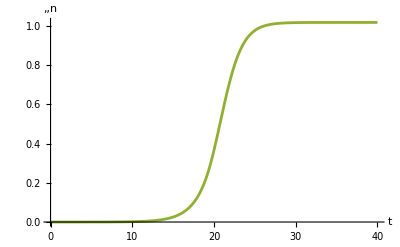

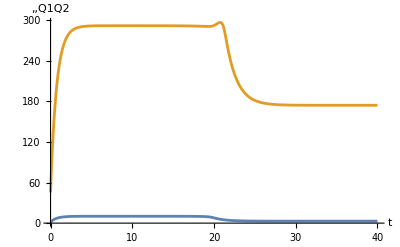

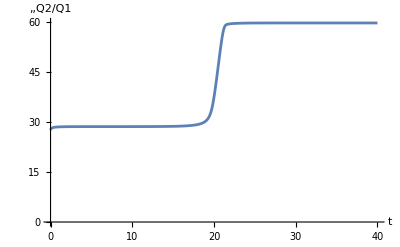

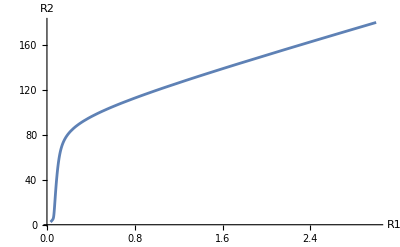

```mathematica
(* Fig 1 *)
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},40];
PlotDynamics[sol,{n}]
PlotDynamics[sol,{Q1,Q2}]
PlotDynamics[sol,{Q2/Q1},PlotRange->{0,60}]
PlotTrajectory[sol,{R1,R2}]
```

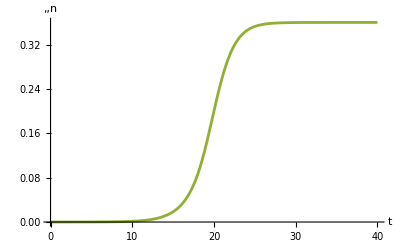

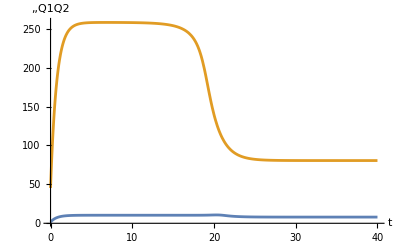

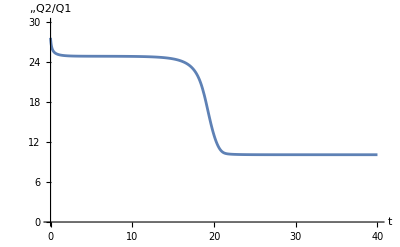

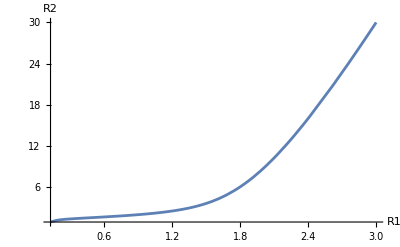

```mathematica
(* Fig 2 *)
Rin2=30;
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},40];
PlotDynamics[sol,{n}]
PlotDynamics[sol,{Q1,Q2}]
PlotDynamics[sol,{Q2/Q1},PlotRange->{0,30}]
PlotTrajectory[sol,{R1,R2}]
```

### Fig 3

```mathematica
μ[Q1_,Q2_]:=NMin[μ1[Q1],μ2[Q2]];
```

```mathematica
a=0.59;Rin2=30;
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},100];
```

```mathematica
Clear[Rin2]
tr=TrackEcoEq[FinalSlice[sol],Rin2->30,{Rin2,1,180},SMax->1000];
```

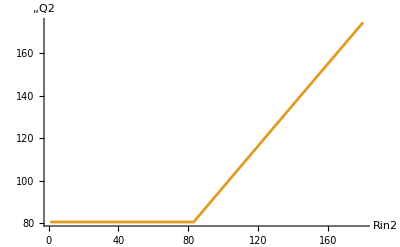

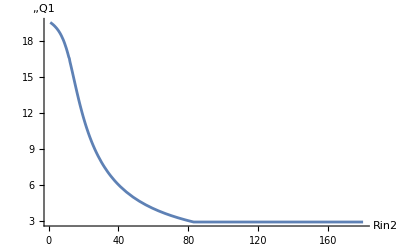

```mathematica
PlotEcoEq[tr,{Q2}]
PlotEcoEq[tr,{Q1}]
```

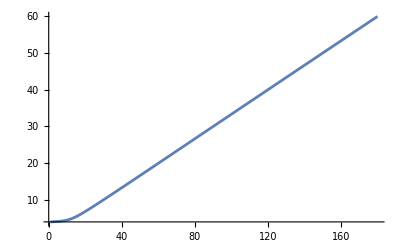

```mathematica
Plot[Q2/Q1/.tr,{Rin2,0,180},PlotRange->All]
```

### Fig 4A

```mathematica
a=0.59;Rin2=10Rin1;
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},100];
Clear[a];
tr10=TrackEcoEq[FinalSlice[sol],a->0.59,{a,0,1.11},SMax->1000];
```

TrackEq::chst: Stability change at a=6.07922×10^-7, eigenvalues={-37.592,-37.2216,-1.35,-1.39216×10^-6,0}.

```mathematica
a=0.59;Rin2=27.7Rin1;
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},100];
Clear[a];
tr27=TrackEcoEq[FinalSlice[sol],a->0.59,{a,0,1.11},SMax->1000];
```

TrackEq::chst: Stability change at a=4.81618×10^-6, eigenvalues={-104.166,-103.138,-1.35,-4.93329×10^-6,0}.

```mathematica
a=0.59;Rin2=60Rin1;
sol=EcoSim[{R1->Rin1,R2->Rin2,Q1->Qmin1,Q2->Qmin2,n->10^-5},100];
Clear[a];
tr60=TrackEcoEq[FinalSlice[sol],a->0.59,{a,0,1.11},SMax->1000];
```

TrackEq::chst: Stability change at a=6.90518×10^-6, eigenvalues={-104.025,-102.998,-1.35,-7.80318×10^-6,0}.

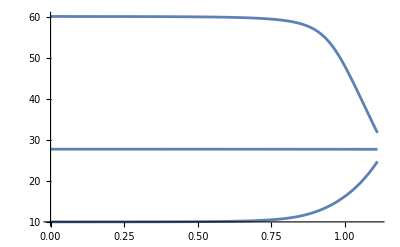

```mathematica
Plot[Q2/Q1/.{tr10[[1]],tr27[[1]],tr60[[1]]},{a,0,1.2},PlotRange->All]
```

### Piecewise

```mathematica
Clear[Rin2];
μ[Q1_,Q2_]:=μ1[Q1];
eq1=SolveEcoEq[];
μ[Q1_,Q2_]:=μ2[Q2];
eq2=SolveEcoEq[];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Solve[0==n/.eq1[[2]],a]
Solve[0==n/.eq2[[2]],a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→1.13255},{a→1.35}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→1.35},{a→(32882.1 Rin2)/(24516.+28735. Rin2)}}

```mathematica
amax=a/.Solve[0==n/.eq[[2]],a][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.13255

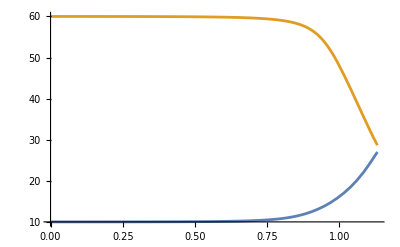

```mathematica
Plot[{
Q2/Q1/.eq2[[2]]/.Rin2->30,
Q2/Q1/.eq1[[2]]/.Rin2->180
},{a,0,amax},PlotRange->All]
```

### Fig 5

```mathematica
a=0.59;
```

```mathematica
Rin1s=Subdivide[1,3,9];
Rin2s=Subdivide[80,10,9];
```

```mathematica
sols=Table[
Rin1=Rin1s[[i]];Rin2=Rin2s[[i]];
EcoSim[{n->1,Q1->Qmin1,Q2->Qmin2,R1->Rin1,R2->Rin2},100]
,{i,1,9,1}];
```

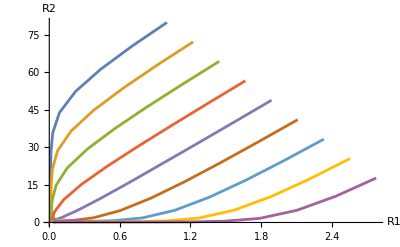

```mathematica
PlotTrajectory[sols,{R1,R2}]
```

## Temperature-response curves

### Gaussian

```mathematica
μ[T_,Topt_]:=μ∞ E^(-(T-Topt)^2/(2σ^2));
Rstar[T_,Topt_]:=m/μ[T,Topt];
```

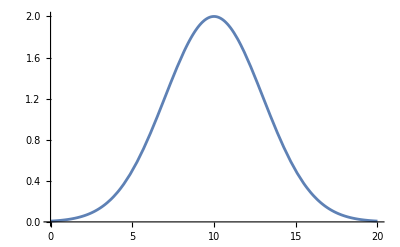

```mathematica
μ∞=2;m=0.2;σ=3;
Plot[μ[T,10],{T,0,20},Ticks->None]
```

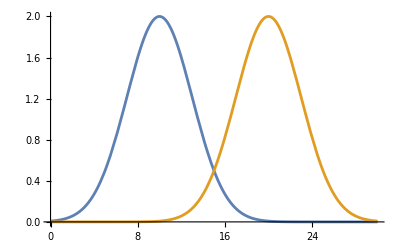

```mathematica
Plot[Evaluate[Table[μ[T,Topt],{Topt,{10,20}}]],{T,0,30},Ticks->None]
```

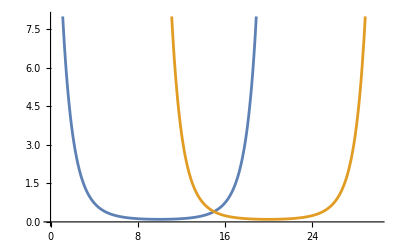

```mathematica
Plot[Evaluate[Table[Rstar[T,Topt],{Topt,{10,20}}]],{T,0,30},PlotRange->{{0,30},{0,8}},Ticks->None]
```

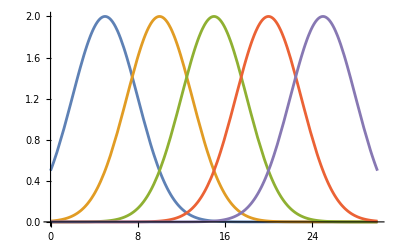

```mathematica
Plot[Evaluate[Table[μ[T,Topt],{Topt,5,25,5}]],{T,0,30},Ticks->None]
```

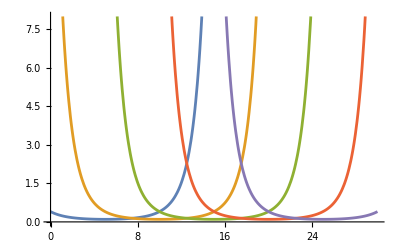

```mathematica
Plot[Evaluate[Table[Rstar[T,Topt],{Topt,5,25,5}]],{T,0,30},PlotRange->{0,8},Ticks->None]
```

### Norberg

```mathematica
Clear[μ∞];
μ∞[T_]:=a E^(b T);
μ[T_,Topt_]:=μ∞[T] (1-((T-Topt)/(w/2))^2);
Rstar[T_,Topt_]:=m/μ[T,Topt];
```

```mathematica
w=10;
a=0.1;b=0.12;
```

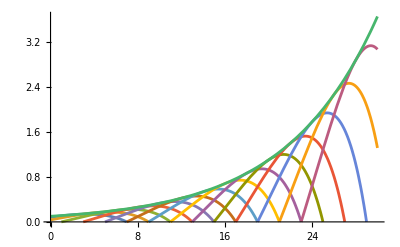

```mathematica
Plot[{Evaluate[Table[μ[T,Topt],{Topt,2,28,2}]],μ∞[T]},{T,0,30},PlotRange->{0,All},Ticks->None]
```

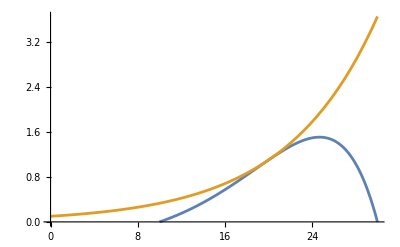

```mathematica
w=20;Plot[{Evaluate[Table[μ[T,Topt],{Topt,20,20}]],μ∞[T]},{T,0,30},PlotRange->{0,All},Ticks->None]
```